```mathematica
Clear["Global`*"]
```

```mathematica
n=100;
J=22/n;
hplus=-5;
hminus=-15;
NSolve[m==1/4(1+Tanh[(hplus+J n m)/2])+1/4(1+Tanh[(hminus+J n m)/2]),m,Reals]
```

{{m→0.00362216},{m→0.214133},{m→0.510222},{m→0.638017},{m→0.99954}}

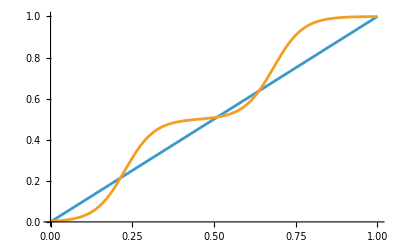

```mathematica
Plot[{m,1/4(1+Tanh[1/2(hplus+J n m)])+1/4(1+Tanh[1/2(hminus+J n m)])},{m,0,1}]
```

```mathematica
(*Define constants*)
J=22/100; (*Fixed coupling constant-adjust this value as needed*)
hdelta=5;

(*Define the equation as a function*)
eqn[n_,hmean_,hdelta_,m_]:=m-(1/4 (1+Tanh[1/2(hmean+hdelta+J  n m)])+1/4 (1+Tanh[1/2(hmean-hdelta+J n m)]))

(*Function to find all real solutions for given n and hplus*)
findSolutions[n_,hmean_]:=Module[{sols,validSols},sols=NSolve[eqn[n,hmean,hdelta,m]==0&&0<=m<=1,m,Reals];
validSols=m/. sols;
(*Pad with NaN if fewer than expected solutions*)
PadRight[validSols,5,Undefined]]
```

```mathematica
(*Define parameter ranges*)
nRange={10,1000};
hmeanRange={-15,-5};

(*Create a grid of parameter values*)
nVals=PowerRange[nRange[[1]],nRange[[2]],1.05];
hmeanVals=Range[hmeanRange[[1]],hmeanRange[[2]],0.05];

(*Calculate solutions for all parameter combinations*)
solutionData=Table[{n,hmean,findSolutions[n,hmean]},{n,nVals},{hmean,hmeanVals}];

(*Extract individual solution surfaces*)
extractSurface[solutionIndex_]:=Flatten[Table[With[{sols=solutionData[[i,j,3]]},If[Length[sols]>=solutionIndex&&NumericQ[sols[[solutionIndex]]],{solutionData[[i,j,1]],solutionData[[i,j,2]],sols[[solutionIndex]]},Nothing]],{i,Length[nVals]},{j,Length[hmeanVals]}],1];

(*Get data for up to 3 solution branches*)
surface1=extractSurface[1];
surface2=extractSurface[2];
surface3=extractSurface[3];
surface4=extractSurface[4];
surface5=extractSurface[5];
```

```mathematica
ListPointPlot3D[{surface1,surface2,surface3,surface4,surface5},ScalingFunctions->{"Log",None,None},AxesLabel->{"n","h","m"},PlotStyle->PointSize[.01]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Define the equation as a function*)
susceptibility[n_,hmean_,hdelta_,m_,mp_]:=mp-1/8 J(m+n mp) (Sech[1/2(hmean+hdelta+J  n m)]^2+Sech[1/2(hmean-hdelta+J n m)]^2);

(*Function to find all real solutions for given n, hplus, m_*)
findSusceptbility[n_,hmean_,m_]:=Module[{sols,validSols},sols=NSolve[susceptibility[n,hmean,hdelta,m,mp]==0,mp,Reals];
validSols=mp/. sols]
```

```mathematica
(*Extract individual solution surfaces*)
extractSusSurface[solutionData_]:=Table[With[{sols=solutionData[[i]][[3]]},{solutionData[[i]][[1]],solutionData[[i]][[2]],sols[[1]]}],{i,Length[solutionData]}];

(*Calculate solutions for all parameter combinations*)
solutionData=Table[{params[[1]],params[[2]],findSusceptbility[params[[1]],params[[2]],params[[3]]]},{params,surface1}];
susSurface1=extractSusSurface[solutionData];
solutionData=Table[{params[[1]],params[[2]],findSusceptbility[params[[1]],params[[2]],params[[3]]]},{params,surface2}];
susSurface2=extractSusSurface[solutionData];
solutionData=Table[{params[[1]],params[[2]],findSusceptbility[params[[1]],params[[2]],params[[3]]]},{params,surface3}];
susSurface3=extractSusSurface[solutionData];
```

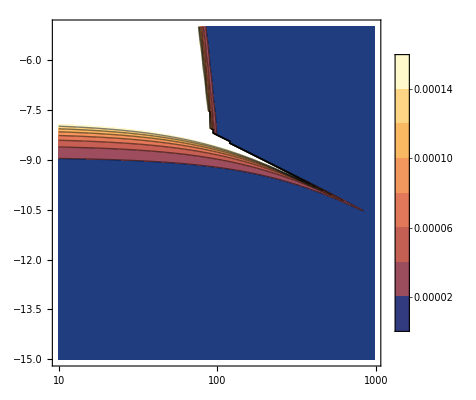

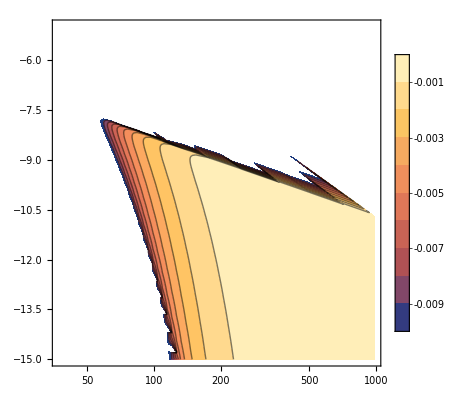

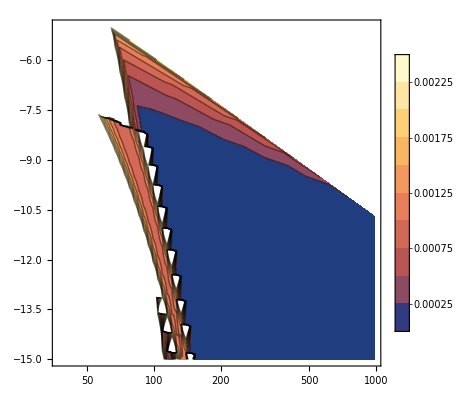

```mathematica
ListContourPlot[susSurface1,PlotLegends->Automatic,ScalingFunctions->{"Log",None},InterpolationOrder->1]
ListContourPlot[susSurface2,PlotLegends->Automatic,ScalingFunctions->{"Log",None},InterpolationOrder->1]
ListContourPlot[susSurface3,PlotLegends->Automatic,ScalingFunctions->{"Log",None}]
```

#### Additional plotting tools

```mathematica
(*Optional:Interactive manipulation*)
Manipulate[With[{sols=findSolutions[n,hplus]},Column[{Plot[{1/4 (1+Tanh[hplus+2 J (n-1) m])+1/4 (1+Tanh[hminus+2 J (n-1) m]),m},{m,-2,2},PlotStyle->{Blue,Red},PlotLegends->{"RHS","LHS"},PlotLabel->"Graphical solution (J = "<>ToString[J]<>")",Epilog->{PointSize[Large],Black,Point[Table[{sol,sol},{sol,DeleteCases[sols,Undefined]}]]}],"Solutions: "<>ToString[DeleteCases[sols,Undefined]]}]],{n,50,200,5},{hplus,-5,1,0.1},{hminus,-10,-1,0.1}]

(*Additional:Explore different J values*)
Manipulate[Module[{eqnJ,solsJ},eqnJ[n_,hplus_,m_]:=m-(1/4 (1+Tanh[hplus+2 Jval (n-1) m])+1/4 (1+Tanh[hminus+2 Jval (n-1) m]));
solsJ=m/. NSolve[eqnJ[n,hplus,m]==0&&-2<=m<=2,m,Reals];
Plot[{1/4 (1+Tanh[hplus+2 Jval (n-1) m])+1/4 (1+Tanh[hminus+2 Jval (n-1) m]),m},{m,-2,2},PlotStyle->{Blue,Red},PlotLegends->{"RHS","LHS"},PlotLabel->"Effect of J on solutions (J = "<>ToString[Jval]<>")",Epilog->{PointSize[Large],Black,Point[Table[{sol,sol},{sol,solsJ}]]}]],{Jval,0.01,1,0.01},{n,50,200,5},{hplus,-5,1,0.1},{hminus,-10,-1,0.1}]
```